## Solving the Kolovsky equation

```mathematica
(*Prelims. Gravity defined in units of Energy recoil Er=ℏ^2 π^2/2m for Rubidium 69
kr is half width of the first Brillouin zone. 
nb is number of bands. n is discretisation across FBZ. A1, A2 and ϕ are superlattice params.
*)
grav=.354692 4;trunc=20;kr=π/4;nb=5;n=5000;F=.01grav;A1=3.;A2=2.;ϕ=0/8;
fbz=Range[0,2kr,2kr/n][[1;;n]]//N;
Δk=fbz[[2]];
Δt=Δk/F;
```

```mathematica
(*Equation 13 in the screenshot below is the first-order ode we are seeking to solve.*)
Framed[Import["Desktop/GitHub/MMWOS/klvsky.png"]]
```

-Graphics-

```mathematica
(*Eigensystem*)
H[κ_]=SparseArray[{{r_,r_}/;r≤trunc->((κ/π-1/2 trunc+1/2(r-1))^2-A1/2 - A2/2),{r_,r_}/;r==trunc+1->(κ/π+0)^2-A1/2 - A2/2,{r_,r_}/;r>trunc+1->(κ/π+1/2(r-trunc-1))^2-A1/2 - A2/2,{r_,c_}/;Abs[r-c]==4->-A1/4,{r_,c_}/;r-c==-5->-1/4 A2 ⅇ^(2 ⅈ ϕ),{r_,c_}/;r-c==5->-1/4 A2 ⅇ^(-2 ⅈ ϕ)},{2trunc+1,2trunc+1}];
reducedH[κ_]=H[κ]-IdentityMatrix[2trunc+1]*10^3;
values={};vectors={};
Do[
{e,v}=-Eigensystem[-reducedH[fbz[[i]]],10,Method->{"Arnoldi",Criteria->RealPart}];

(*Quantum phase correction*)
Do[
α=Arg[v[[jk,trunc]]];
v[[jk]] = v[[jk]] Exp[-I α];
,{jk,10}];

AppendTo[values,e+10^3];
AppendTo[vectors,v];
,{i,1,n}];
```

```mathematica
(*this block numerically defines the Subscript[X, α,β] functions. To be interpolated later. We require only the upper half of the matrix (i.e. Subscript[X, 1,2], Subscript[X, 1,3].... and not Subscript[X, 2,1] etc.)
Noticably we aren't performing the integration; it takes place in real space and we are operating in momentum space. 
These are defined only in the first Brillouin zone to save computation time. 
*)
XFn={};
Bands=5;TotalXFns=Bands(Bands-1)/2;
ranges=Table[Range[2+k,Bands],{k,0,Bands-2}];
For[counter=1,counter≤Length[ranges],counter++,
Temperer={};
Do[
Temp={};
Do[
(*nd for "numerical differentiation"*)
nd=(vectors[[i+1,bandval]]-vectors[[i-1,bandval]])/(2Δk);
AppendTo[Temp,nd.(vectors[[i,counter]]*)];
,{i,2,n-1}];
nX=Abs[Join[{2Temp[[1]]-Temp[[2]]},Temp,{2Temp[[n-3]]-Temp[[n-2]]}]];
AppendTo[Temperer,nX];
,{bandval,ranges[[counter]]}
];
AppendTo[XFn,Temperer]
]
```

```mathematica
(*np=Number of half periods to take. This will let us know how far to evolve the dynamics for. Tf is the final time.*)
np=10;Tf=np kr/F;
(*Full Momentum Space Spanned*)
momenta=Table[k,{k,0,np kr,Δk}][[1;;n np/2]];
(*Overlaps
This block gives us the overlap functions Subscript[X, α,β] across the whole space we are evolving over.
*)
FR={};
For[i=1,i≤Length[XFn],i++,
Temp={};
SubX=XFn[[i]];
For[jj=1,jj≤Length[SubX],jj++,
SubSubX=SubX[[jj]];
dx=Table[{momenta[[it]],SubSubX[[Mod[it,n,1]]]},{it,n np/2}];
AppendTo[Temp,dx];
];
AppendTo[FR,Temp];
];

Quiet[Do[
Evaluate[ToExpression["X"<>ToString[k]<>ToString[l]]]=Interpolation[FR[[k,l-k]]];
,{k,1,Bands-1},{l,k+1,Bands}];];
(*Giving the energy bands an x-axis value, again, across the whole number of brillouin zones spanned.*)
EnergyBands={};Do[
BandX=Table[{momenta[[i]],valuesᵀ[[k,Mod[i,n,1]]]},{i,n np/2}];
AppendTo[EnergyBands,BandX];
,{k,1,Bands}];

(*Defining the phase terms in the Kolovsky equation*)
Do[
data=EnergyBands[[B]];
var=ToExpression["Ef"<>ToString[B]];
Evaluate[var][k_]=Fit[data,Table[Cos[m 4k],{m,0,10}],k];
,{B,1,Bands}];
Do[var=ToExpression["Ph"<>ToString[k]<>ToString[l]];
Evaluate[var][t_]=Exp[- ⅈ Integrate[((ToExpression["Ef"<>ToString[k]])[F τ]-(ToExpression["Ef"<>ToString[l]])[F τ]),{τ,0,t}]];
,{k,1,Bands-1},{l,k+1,Bands}];
```

```mathematica
A=ConstantArray[0,{Bands,Bands}];
Do[If[l≤k,0,
XTerm=ToExpression["X"<>ToString[k]<>ToString[l]];
PTerm=ToExpression["Ph"<>ToString[k]<>ToString[l]];
A[[k,l]]=XTerm[F t] PTerm[t];
]
,{k,Bands},{l,Bands}];
A=F(A+A†);
initc={c1[0]==1,c2[0]==0,c3[0]==0,c4[0]==0,c5[0]==0};
c={c1[t],c2[t],c3[t],c4[t],c5[t]};
eee= ⅈ D[c,t]-A.c;
eq=Table[eee[[i]]==0,{i,nb}];
sol=NDSolve[{Join[eq,initc]},{c1[t],c2[t],c3[t],c4[t],c5[t]},{t,0,Tf}];
max[i_]:=Table[populations[[i]],{t,0,Tf,Δt}]//Max;
populations=Abs[(c/.sol)[[1]]]^2;
```

InterpolatingFunction::dmval: Input value {7.85398} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

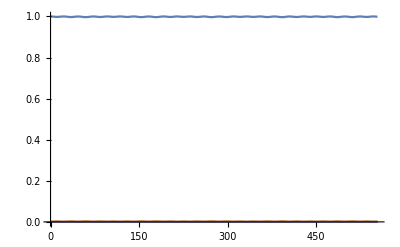

```mathematica
Plot[populations,{t,0,Tf}]
```

## Collected Function for plotting

```mathematica
grav=.354692 4;trunc=20;kr=π/4;nb=5;
```

### Function viewpopulations[a1,a2,phi, force,periods]

```mathematica
viewpopulations[a1_,a2_,phi_,force_,periods_]:=(
n=If[a1<1||a2<1,10000,2000];F=force;A1=a1;A2=a2;ϕ=phi;kr=π/4;

fbz=Range[0,2kr,2kr/n][[1;;n]]//N;
Δk=fbz[[2]];
Δt=Δk/F;
H[κ_]=SparseArray[{{r_,r_}/;r≤trunc->((κ/π-1/2 trunc+1/2(r-1))^2-A1/2 - A2/2),{r_,r_}/;r==trunc+1->(κ/π+0)^2-A1/2 - A2/2,{r_,r_}/;r>trunc+1->(κ/π+1/2(r-trunc-1))^2-A1/2 - A2/2,{r_,c_}/;Abs[r-c]==4->-A1/4,{r_,c_}/;r-c==-5->-1/4 A2 ⅇ^(2 ⅈ ϕ),{r_,c_}/;r-c==5->-1/4 A2 ⅇ^(-2 ⅈ ϕ)},{2trunc+1,2trunc+1}];
reducedH[κ_]=H[κ]-IdentityMatrix[2trunc+1]*10^3;
values={};vectors={};
Do[
{e,v}=-Eigensystem[-reducedH[fbz[[i]]],10,Method->{"Arnoldi",Criteria->RealPart}];

(*Quantum phase correction*)
Do[
α=Arg[v[[jk,trunc]]];
v[[jk]] = v[[jk]] Exp[-I α];
,{jk,10}];

AppendTo[values,e+10^3];
AppendTo[vectors,v];
,{i,1,n}];
XFn={};
Bands=5;TotalXFns=Bands(Bands-1)/2;
ranges=Table[Range[2+k,Bands],{k,0,Bands-2}];
For[counter=1,counter≤Length[ranges],counter++,
Temperer={};
Do[
Temp={};
Do[
(*nd for "numerical differentiation"*)
nd=(vectors[[i+1,bandval]]-vectors[[i-1,bandval]])/(2Δk);
AppendTo[Temp,nd.(vectors[[i,counter]]*)];
,{i,2,n-1}];
nX=Abs[Join[{2Temp[[1]]-Temp[[2]]},Temp,{2Temp[[n-3]]-Temp[[n-2]]}]];
AppendTo[Temperer,nX];
,{bandval,ranges[[counter]]}
];
AppendTo[XFn,Temperer]
];

np=2*periods;Tf=np kr/F;
(*Full Momentum Space Spanned*)
FR={};
For[i=1,i≤Length[XFn],i++,
Temp={};
SubX=XFn[[i]];
For[jj=1,jj≤Length[SubX],jj++,
SubSubX=SubX[[jj]];
dx=Table[{momenta[[it]],SubSubX[[Mod[it,n,1]]]},{it,n np/2}];
AppendTo[Temp,dx];
];
AppendTo[FR,Temp];
];

Quiet[Do[
Evaluate[ToExpression["X"<>ToString[k]<>ToString[l]]]=Interpolation[FR[[k,l-k]]];
,{k,1,Bands-1},{l,k+1,Bands}];];
(*Giving the energy bands an x-axis value, again, across the whole number of brillouin zones spanned.*)
EnergyBands={};Do[
BandX=Table[{momenta[[i]],valuesᵀ[[k,Mod[i,n,1]]]},{i,n np/2}];
AppendTo[EnergyBands,BandX];
,{k,1,Bands}];

(*Defining the phase terms in the Kolovsky equation*)
Do[
data=EnergyBands[[B]];
var=ToExpression["Ef"<>ToString[B]];
Evaluate[var][k_]=Fit[data,Table[Cos[m 4k],{m,0,10}],k];
,{B,1,Bands}];
Do[var=ToExpression["Ph"<>ToString[k]<>ToString[l]];
Evaluate[var][t_]=Exp[- ⅈ Integrate[((ToExpression["Ef"<>ToString[k]])[F τ]-(ToExpression["Ef"<>ToString[l]])[F τ]),{τ,0,t}]];
,{k,1,Bands-1},{l,k+1,Bands}];
initialtime=(0/(4F));

A=ConstantArray[0,{Bands,Bands}];
Do[If[l≤k,0,
XTerm=ToExpression["X"<>ToString[k]<>ToString[l]];
PTerm=ToExpression["Ph"<>ToString[k]<>ToString[l]];
A[[k,l]]=XTerm[F t] PTerm[t];
]
,{k,Bands},{l,Bands}];
A=F(A+A†);
initc={c1[initialtime]==1,c2[initialtime]==0,c3[initialtime]==0,c4[initialtime]==0,c5[initialtime]==0};
c={c1[t],c2[t],c3[t],c4[t],c5[t]};
eee= ⅈ D[c,t]-A.c;
eq=Table[eee[[i]]==0,{i,nb}];
sol=NDSolve[{Join[eq,initc]},{c1[t],c2[t],c3[t],c4[t],c5[t]},{t,initialtime,Tf}];
max[i_]:=Table[populations[[i]],{t,initialtime,Tf,Δt}]//Max;
populations=Abs[(c/.sol)[[1]]]^2;
Plot[populations,{t,initialtime,Tf},PlotRange->{0,1}])
```

### Using function

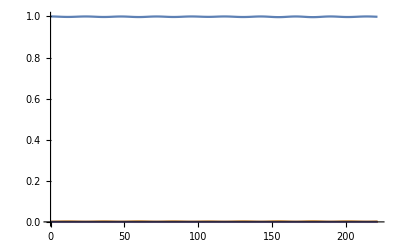

```mathematica
viewpopulations[3,2,0/8,.01grav,2]
```

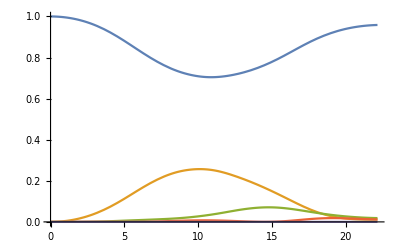

```mathematica
viewpopulations[3,2,0/8,.1grav,2]
```

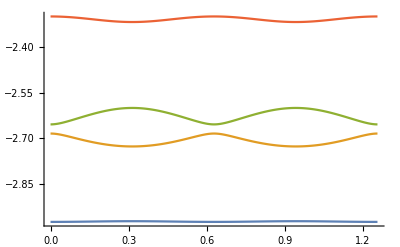

```mathematica
ListPlot[EnergyBands[[1;;4]],Joined->True]
```

## Code dump; not pretty

### If kernel has cleared, skip to next section.

```mathematica
grav=.354692 4;trunc=16;kr=π/4;nb=5;
beamsplitterfn[levels_,force_]:=(list={};
(*If[levels[[1]]==1||levels[[1]]==3,ϕ=π/8,ϕ=0];*)
Do[

Do[n=If[A1<1||A2<1,10000,2000];F=force;(*A1=a1;A2=a2;ϕ=phi;*)
H[κ_]=SparseArray[{{i_,i_}/;i≤trunc->((κ/π-1/2 trunc+1/2(i-1))^2-A1/2 - A2/2),{i_,i_}/;i==trunc+1->(κ/π+0)^2-A1/2 - A2/2,{i_,i_}/;i>trunc+1->(κ/π+1/2(i-trunc-1))^2-A1/2 - A2/2,{i_,j_}/;Abs[i-j]==4->-A1/4,{i_,j_}/;i-j==-5->-1/4 A2 ⅇ^(2 ⅈ ϕ),{i_,j_}/;i-j==5->-1/4 A2 ⅇ^(-2 ⅈ ϕ)},{2.trunc+1.,2.trunc+1.}];
reducedH[κ_]=H[κ]-IdentityMatrix[2trunc+1]*10^3;
fbz=Range[0,2kr,2kr/n][[1;;n]]//N;
Δk=fbz[[2]];
Δt=Δk/F;
values={};vectors={};
Do[
{e,v}=-Eigensystem[-reducedH[fbz[[i]]],10,Method->{"Arnoldi",Criteria->RealPart}];

Do[
α=Arg[v[[jk,trunc]]];
v[[jk]] = v[[jk]] Exp[-I α];

,{jk,10}];
Table[If[i>1&&Abs[(v[[ij]]-Last[vectorsᵀ[[ij]]])//Total]>1,v[[ij]]=-v[[ij]]],{ij,1,nb}];
AppendTo[values,e+10^3];
AppendTo[vectors,v];,
{i,1,n}];
x12={};
Do[nd=(vectors[[i+1,2]]-vectors[[i-1,2]])/(2Δk);
AppendTo[x12,nd.(vectors[[i,1]]*)];,{i,2,n-1}];
nx12=Join[{2x12[[1]]-x12[[2]]},x12,{-x12[[n-3]]+2x12[[n-2]]}];

x13={};
Do[nd=(vectors[[i+1,3]]-vectors[[i-1,3]])/(2Δk);
AppendTo[x13,nd.(vectors[[i,1]]*)];,{i,2,n-1}];
nx13=Join[{2x13[[1]]-x13[[2]]},x13,{-x13[[n-3]]+2x13[[n-2]]}];

x14={};
Do[nd=(vectors[[i+1,4]]-vectors[[i-1,4]])/(2Δk);
AppendTo[x14,nd.(vectors[[i,1]]*)];,{i,2,n-1}];
nx14=Join[{2x14[[1]]-x14[[2]]},x14,{2x14[[n-3]]-x14[[n-2]]}];

x15={};
Do[nd=(vectors[[i+1,5]]-vectors[[i-1,5]])/(2Δk);
AppendTo[x15,nd.(vectors[[i,1]]*)];,{i,2,n-1}];
nx15=Join[{2x15[[1]]-x15[[2]]},x15,{2x15[[n-3]]-x15[[n-2]]}];

x23={};
Do[nd=(vectors[[i+1,3]]-vectors[[i-1,3]])/(2Δk);
AppendTo[x23,nd.(vectors[[i,2]]*)];,{i,2,n-1}];
nx23=Join[{2x23[[1]]-x23[[2]]},x23,{-x23[[n-3]]+2x23[[n-2]]}];

x24={};
Do[nd=(vectors[[i+1,4]]-vectors[[i-1,4]])/(2Δk);
AppendTo[x24,nd.(vectors[[i,2]]*)];,{i,2,n-1}];
nx24=Join[{2x24[[1]]-x24[[2]]},x24,{2x24[[n-3]]-x24[[n-2]]}];

x25={};
Do[nd=(vectors[[i+1,5]]-vectors[[i-1,5]])/(2Δk);
AppendTo[x25,nd.(vectors[[i,2]]*)];,{i,2,n-1}];
nx25=Join[{2x25[[1]]-x25[[2]]},x25,{2x25[[n-3]]-x25[[n-2]]}];

x34={};
Do[nd=(vectors[[i+1,4]]-vectors[[i-1,4]])/(2Δk);
AppendTo[x34,nd.(vectors[[i,3]]*)];,{i,2,n-1}];
nx34=Join[{2x34[[1]]-x34[[2]]},x34,{2x34[[n-3]]-x34[[n-2]]}];
x35={};
Do[nd=(vectors[[i+1,5]]-vectors[[i-1,5]])/(2Δk);
AppendTo[x35,nd.(vectors[[i,3]]*)];,{i,2,n-1}];
nx35=Join[{2x35[[1]]-x35[[2]]},x35,{2x35[[n-3]]-x35[[n-2]]}];

x45={};
Do[nd=(vectors[[i+1,5]]-vectors[[i-1,5]])/(2Δk);
AppendTo[x45,nd.(vectors[[i,4]]*)];,{i,2,n-1}];
(*x45=-Abs[x45];*)
nx45=Join[{2x45[[1]]-x45[[2]]},x45,{2x45[[n-3]]-x45[[n-2]]}];
(*Landau Zener formula*)
gap[i_,j_]:=If[EvenQ[i],values[[1,j]]-values[[1,i]],values[[n/2,j]]-values[[n/2,i]]];
lz[i_,j_]:=(*ⅇ^(-π^3 gap[i,j]^2/(i 8 F))*)ⅇ^((- 4 gap[i,j]^2)/(i F));
(*Number of half periods to take*)np=4;Tf=np kr/F;
(*Full Momentum Space Spanned*)
numericalxlists={nx12,nx13,nx14,nx15,nx23,nx24,nx25,nx34,nx35,nx45};
momenta=Table[k,{k,0,np kr,Δk}][[1;;n np/2]];

fullrange={dx12,dx13,dx14,dx15,dx23,dx24,dx25,dx34,dx35,dx45}={Table[{momenta[[i]],nx12[[Mod[i,n,1]]]},{i,n np/2}],Table[{momenta[[i]],nx13[[Mod[i,n,1]]]},{i,n np/2}],Table[{momenta[[i]],nx14[[Mod[i,n,1]]]},{i,n np/2}],Table[{momenta[[i]],nx15[[Mod[i,n,1]]]},{i,n np/2}],Table[{momenta[[i]],nx23[[Mod[i,n,1]]]},{i,n np/2}],Table[{momenta[[i]],nx24[[Mod[i,n,1]]]},{i,n np/2}],Table[{momenta[[i]],nx25[[Mod[i,n,1]]]},{i,n np/2}],Table[{momenta[[i]],nx34[[Mod[i,n,1]]]},{i,n np/2}],Table[{momenta[[i]],nx35[[Mod[i,n,1]]]},{i,n np/2}],
Table[{momenta[[i]],nx45[[Mod[i,n,1]]]},{i,n np/2}]};

correctingtable=Table[Table[If[Re[Sign[fullrange[[part]][[ i n,2]]]]=!=Re[Sign[fullrange[[part]][[i n+1,2]]]],fullrange[[part]][[i n+1;;(i+1)n,2]]=-fullrange[[part]][[i n+1;;(i+1)n,2]]],{i,1,np/2-1}],{part,{3,5,7}}];

overlaps={X12,X13,X14,X15,X23,X24,X25,X34,X35,X45}=Table[Interpolation[fullrange[[i]]],{i,1,Length[fullrange]}];
(*plotsRe=Table[Plot[overlaps[[i]][F t]//Re,{t,0,Tf},PlotRange->All,PlotStyle->If[i==1||i==5||i==8||i==10,Red,Blue]],{i,Length[overlaps]}];
plotsIm=Table[Plot[overlaps[[i]][F t]//Im,{t,0,Tf},PlotRange->All,PlotStyle->If[i==1||i==5||i==8||i==10,Red,Blue]],{i,Length[overlaps]}];*)

energy={ev1,ev2,ev3,ev4,ev5}=Table[Table[{momenta[[ii]],valuesᵀ[[bi,Mod[ii,n,1]]]},{ii,n np/2}],{bi,nb}];
bands[k_]={e1[k_],e2[k_],e3[k_],e4[k_],e5[k_]}=Table[Fit[energy[[bi]],Table[Cos[m 4k],{m,0,10}],k],{bi,nb}];
phases[t_]={p12[t],p13[t],p14[t],p15[t],p23[t],p24[t],p25[t],p34[t],p35[t],p45[t]}={Exp[- ⅈ Integrate[e1[F τ]-e2[F τ],{τ,0,t}]],Exp[- ⅈ Integrate[e1[F τ]-e3[F τ],{τ,0,t}]],Exp[- ⅈ Integrate[e1[F τ]-e4[F τ],{τ,0,t}]],Exp[- ⅈ Integrate[e1[F τ]-e5[F τ],{τ,0,t}]],Exp[- ⅈ Integrate[e2[F τ]-e3[F τ],{τ,0,t}]],Exp[- ⅈ Integrate[e2[F τ]-e4[F τ],{τ,0,t}]],Exp[- ⅈ Integrate[e2[F τ]-e5[F τ],{τ,0,t}]],Exp[- ⅈ Integrate[e3[F τ]-e4[F τ],{τ,0,t}]],Exp[- ⅈ Integrate[e3[F τ]-e5[F τ],{τ,0,t}]],Exp[- ⅈ Integrate[e4[F τ]-e5[F τ],{τ,0,t}]]};

(*phplotsRe=Table[Plot[phases[t][[i]]//Re,{t,0,Tf},PlotRange->All,PlotStyle->If[i==1||i==5||i==8||i==10,Red,Blue]],{i, Length[phases[t]]}];
phplotsIm=Table[Plot[phases[t][[i]]//Im,{t,0,Tf},PlotRange->All,PlotStyle->If[i==1||i==5||i==8||i==10,Red,Blue]],{i, Length[phases[t]]}];
phplotsAbs=Table[Plot[Abs[phases[t][[i]]],{t,0,Tf},PlotRange->All,PlotStyle->If[i==1||i==5||i==8||i==10,Red,Blue]],{i, Length[phases[t]]}];*)

If[levels[[1]]==1||levels[[1]]==3,{it=0,ft=Tf/2},{it=π/(4F),ft=3π/(4F)}];
start=Table[KroneckerDelta[levels[[1]],l],{l,1,nb}];
If[levels[[1]]==1,{k1=1,k2=0,k3=0,k4=0},If[levels[[1]]==2,{k1=0,k2=1,k3=0,k4=0},If[levels[[1]]==3,{k1=0,k2=0,k3=1,k4=0},If[levels[[1]]==4,{k1=0,k2=0,k3=0,k4=1}]]]];(*k1=k2=k3=k4=1;*)

A=  F ({{0, k1 X12[F t]p12[t], X13[F t]p13[t], X14[F t]p14[t], X15[F t]p15[t]}, {k1 X12[F t]*p12[t]*, 0, k2 X23[F t]p23[t], X24[F t]p24[t], X25[F t]p25[t]}, {X13[F t]*p13[t]*, k2 X23[F t]*p23[t]*, 0, k3 X34[F t]p34[t], X35[F t]p35[t]}, {X14[F t]*p14[t]*, X24[F t]*p24[t]*, k3 X34[F t]*p34[t]*, 0, k4 X45[F t]p45[t]}, {X15[F t]*p15[t]*, X25[F t]*p25[t]*, X35[F t]*p35[t]*, k4 X45[F t]*p45[t]*, 0}});
initc={c1[it]==start[[1]],c2[it]==start[[2]],c3[it]==start[[3]],c4[it]==start[[4]],c5[it]==start[[5]]};
c={c1[t],c2[t],c3[t],c4[t],c5[t]};
eee= ⅈ D[c,t]-A.c;
eq=Table[eee[[hj]]==0,{hj,nb}];
sol1=NDSolve[{Join[eq,initc]},{c1[t],c2[t],c3[t],c4[t],c5[t]},{t,it,ft}];
sol2=NDSolve[{Join[eq,initc]},{c1[t],c2[t],c3[t],c4[t],c5[t]},{t,0,Tf}];
populations1=Abs[(c/.sol1)[[1]]]^2;
populations2=Abs[(c/.sol2)[[1]]]^2;


(*populationoflevelsbelow=If[levels[[1]]>1,Total[populations1[[1;;levels[[1]]-1]]/.t->ft/2],0];
weightedpop=1-populationoflevelsbelow;
populationoflevelsabove=Total[populations1[[levels[[2]];;nb]]/.t->ft];

xferpop=populationoflevelsabove/(weightedpop);

prob=If[levels[[1]]==1,1-(populations1[[1]]/.t->ft),xferpop];*)
popleft=(populations1[[levels[[1]]]]/.t->ft);
prob=1-popleft;

AppendTo[list,{gap[levels[[1]],levels[[2]]],prob}];,{A1,.5,3,.5},{A2,.5,3,.5}];

,{ϕ,{0,(*π/20,*)π/8}}]);
```

```mathematica
listᵀ[[2]]
```

{0.999853,0.999887,0.999424,0.998263,0.995937,0.991928,0.99991,0.998706,0.993883,0.982727,0.962819,0.933481}

```mathematica
Clear[bs23smaller,bs34smaller,bs45smaller,bs12smaller]
```

```mathematica
Timing[beamsplitterfn[{1,2},0.05];bs12=list;Print["1→2 Done"];Export["bs12.nb",bs12];]
Timing[beamsplitterfn[{2,3},0.05];bs23=list;
Print["2→3 Done"];Export["bs23.nb",bs23];]
Timing[beamsplitterfn[{3,4},0.05];bs34=list;Print["3→4 Done"];Export["bs34.nb",bs34];]
Timing[beamsplitterfn[{4,5},0.05];Print["4→5 Done"];Export["bs45.nb",bs45];]
```

InterpolatingFunction::dmval: Input value {3.14159} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

1→2 Done

{4519.84,Null}

InterpolatingFunction::dmval: Input value {3.14146} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

2→3 Done

{4899.71,Null}

InterpolatingFunction::dmval: Input value {3.14159} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

3→4 Done

{4841.63,Null}

InterpolatingFunction::dmval: Input value {3.14159} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

4→5 Done

{4853.11,Null}

```mathematica
{A1,A2,ϕ,i,t}//Dynamic
```

### Start Here if kernel has cleared.

```mathematica
&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&&
```

```mathematica
"Load notebook(s) >>bs(ij)f05.nb<< and run the matrix as 
{{bg12,trans12},{bg23,trans23},{bg34,trans34},{bg45,trans45}}=

If the kernel has cleared."
```

```mathematica
fv=Length[Table[j,{j,.5,2.,.5}]];
sv=Length[Table[j,{j,.5,2,.25}]];
tv=Length[Table[phi,{phi,{0,π/16,π/8}}]];
```

```mathematica
{bg12f05,trans12f05}=Table[Table[bs12f05[[1+j;;(fv sv)+j]][[1+i;;sv+i,1;;2]],{j,0,(fv sv tv)-(fv sv),fv sv},{i,0,(fv sv)-sv,sv}][[All,All,All,i]],{i,1,2}];
fullplots12f05=Table[bs12f05[[1+j;;(fv sv)+j]][[1+i;;sv+i,3]],{j,0,(fv sv tv)-(fv sv),fv sv},{i,0,(fv sv)-sv,sv}];
```

```mathematica
{bg23f05,trans23f05}=Table[Table[bs23f05[[1+j;;(fv sv)+j]][[1+i;;sv+i,1;;2]],{j,0,(fv sv tv)-(fv sv),fv sv},{i,0,(fv sv)-sv,sv}][[All,All,All,i]],{i,1,2}];
fullplots23f05=Table[bs23f05[[1+j;;(fv sv)+j]][[1+i;;sv+i,3]],{j,0,(fv sv tv)-(fv sv),fv sv},{i,0,(fv sv)-sv,sv}];
```

```mathematica
{bg34f05,trans34f05}=Table[Table[bs34f05[[1+j;;(fv sv)+j]][[1+i;;sv+i,1;;2]],{j,0,(fv sv tv)-(fv sv),fv sv},{i,0,(fv sv)-sv,sv}][[All,All,All,i]],{i,1,2}];
fullplots34f05=Table[bs34f05[[1+j;;(fv sv)+j]][[1+i;;sv+i,3]],{j,0,(fv sv tv)-(fv sv),fv sv},{i,0,(fv sv)-sv,sv}];
```

```mathematica
{bg45f05,trans45f05}=Table[Table[bs45f05[[1+j;;(fv sv)+j]][[1+i;;sv+i,1;;2]],{j,0,(fv sv tv)-(fv sv),fv sv},{i,0,(fv sv)-sv,sv}][[All,All,All,i]],{i,1,2}];
fullplots45f05=Table[bs45f05[[1+j;;(fv sv)+j]][[1+i;;sv+i,3]],{j,0,(fv sv tv)-(fv sv),fv sv},{i,0,(fv sv)-sv,sv}];
```

```mathematica
ϕmap[ϕ_]:=If[ϕ==π/8,3,If[ϕ==π/16,2,1]];
a1map[a1_]:=If[a1==0.5,1,2*a1];
a2map[a2_]:=(ts=Solve[a2==0.5+fac(.25),fac];(fac+1)/.ts[[1]])
(*Mappings to convert numerical choices of variables to matrix sections, i.e. ϕ=π/8 corresponds to the Subscript[A, ij]==Subscript[A, 3j] etc. *)
```

```mathematica
{P12[a1_,ϕ_],P23[a1_,ϕ_],P34[a1_,ϕ_],P45[a1_,ϕ_]}:={ListPlot[{trans12[[ϕmap[ϕ],a1map[a1]]]},ImagePadding->45,PlotRange->{All,{0,1}},Frame->{{True,False},{True,True}},DataRange->{.5,2},FrameTicks->{{All,All},{{{.5,"0.5"},{1,"1"},{1.5,"1.5"},{2.,"2."}},None}},PlotStyle->Red,FrameStyle->{{{Red},None},{{Black},{Black}}},ImagePadding->30,PlotRange->All,Joined->True,FrameLabel->{"A_2","T_12"},FrameTicksStyle->{{{Red,15},{15}},{{Black,15},None}},LabelStyle->Directive[ 15],GridLines->{{0.5,0.75,1,1.25,1.5,1.75,2},Automatic}],ListPlot[{trans23[[ϕmap[ϕ],a1map[a1]]]},ImagePadding->45,PlotRange->{All,{0,1}},Frame->{{True,False},{True,True}},DataRange->{.5,2},FrameTicks->{{All,All},{{{.5,"0.5"},{1,"1"},{1.5,"1.5"},{2.,"2."}},None}},PlotStyle->Red,FrameStyle->{{{Red},None},{{Black},{Black}}},ImagePadding->30,PlotRange->All,Joined->True,FrameLabel->{"A_2","T_12"},FrameTicksStyle->{{{Red,15},{15}},{{Black,15},None}},LabelStyle->Directive[ 15],GridLines->{{0.5,0.75,1,1.25,1.5,1.75,2},Automatic}],ListPlot[{trans34[[ϕmap[ϕ],a1map[a1]]]},ImagePadding->45,PlotRange->{All,{0,1}},Frame->{{True,False},{True,True}},DataRange->{.5,2},FrameTicks->{{All,All},{{{.5,"0.5"},{1,"1"},{1.5,"1.5"},{2.,"2."}},None}},PlotStyle->Red,FrameStyle->{{{Red},None},{{Black},{Black}}},ImagePadding->30,PlotRange->All,Joined->True,FrameLabel->{"A_2","T_12"},FrameTicksStyle->{{{Red,15},{15}},{{Black,15},None}},LabelStyle->Directive[ 15],GridLines->{{0.5,0.75,1,1.25,1.5,1.75,2},Automatic}],ListPlot[{trans45[[ϕmap[ϕ],a1map[a1]]]},ImagePadding->45,PlotRange->{All,{0,1}},Frame->{{True,False},{True,True}},DataRange->{.5,2},FrameTicks->{{All,All},{{{.5,"0.5"},{1,"1"},{1.5,"1.5"},{2.,"2."}},None}},PlotStyle->Red,FrameStyle->{{{Red},None},{{Black},{Black}}},ImagePadding->30,PlotRange->All,Joined->True,FrameLabel->{"A_2","T_12"},FrameTicksStyle->{{{Red,15},{15}},{{Black,15},None}},LabelStyle->Directive[ 15],GridLines->{{0.5,0.75,1,1.25,1.5,1.75,2},Automatic}]};
```

```mathematica
{B12[a1_,ϕ_],B23[a1_,ϕ_],B34[a1_,ϕ_],B45[a1_,ϕ_]}:={ListPlot[bg12[[ϕmap[ϕ],a1map[a1]]],ImagePadding->45,Frame->{{False,True},{False,False}},FrameTicks->{{None,All},{All,None}},PlotStyle->Blue,FrameStyle->Blue,ImagePadding->30,PlotRange->{All,All},Joined->False,FrameTicksStyle->{{None,{10}},{None,None}},FrameLabel->{{None,"Δ_12"},{None,None}},LabelStyle->Directive[ 10]],ListPlot[bg23[[ϕmap[ϕ],a1map[a1]]],ImagePadding->45,Frame->{{False,True},{False,False}},FrameTicks->{{None,All},{All,None}},PlotStyle->Blue,FrameStyle->Blue,ImagePadding->30,PlotRange->{All,All},Joined->False,FrameTicksStyle->{{None,{10}},{None,None}},FrameLabel->{{None,"Δ_23"},{None,None}},LabelStyle->Directive[ 10]],ListPlot[bg34[[ϕmap[ϕ],a1map[a1]]],ImagePadding->45,Frame->{{False,True},{False,False}},FrameTicks->{{None,All},{All,None}},PlotStyle->Blue,FrameStyle->Blue,ImagePadding->30,PlotRange->{All,All},Joined->False,FrameTicksStyle->{{None,{10}},{None,None}},FrameLabel->{{None,"Δ_34"},{None,None}},LabelStyle->Directive[ 10]],ListPlot[bg45[[ϕmap[ϕ],a1map[a1]]],ImagePadding->45,Frame->{{False,True},{False,False}},FrameTicks->{{None,All},{All,None}},PlotStyle->Blue,FrameStyle->Blue,ImagePadding->30,PlotRange->{All,All},Joined->False,FrameTicksStyle->{{None,{10}},{None,None}},FrameLabel->{{None,"Δ_45"},{None,None}},LabelStyle->Directive[ 10]]};
```

```mathematica
Compile12[a1_,ϕ_]:=Overlay[{P12[a1,ϕ],B12[a1,ϕ]}];
Compile23[a1_,ϕ_]:=Overlay[{P23[a1,ϕ],B23[a1,ϕ]}];
Compile34[a1_,ϕ_]:=Overlay[{P34[a1,ϕ],B34[a1,ϕ]}];
Compile45[a1_,ϕ_]:=Overlay[{P45[a1,ϕ],B45[a1,ϕ]}];
```

```mathematica
"Range of values includes: A1∈{0.5, 1, 1.5, 2], ϕ∈{0, π/16, π/8}. A2 is plotted over 0.5→2 in steps of 0.25"
```

```mathematica
cc[a1_,ϕ_]:={Compile12[a1,ϕ],Compile23[a1,ϕ],Compile34[a1,ϕ],Compile45[a1,ϕ]};
```

```mathematica
plottab=Table[cc[a1,ϕ][[i]],{a1,{0.5,1,2,3,4,5,6}},{ϕ,{0,π/16,π/8}},{i,1,4}];
pchoice=Transpose[plottab,{2,3,1}];
```

```mathematica
"{T_12,T_23,T_34,T_45},A1,ϕ"
pchoice//Dimensions
```

{T_12,T_23,T_34,T_45},A1,ϕ

{4,7,3}

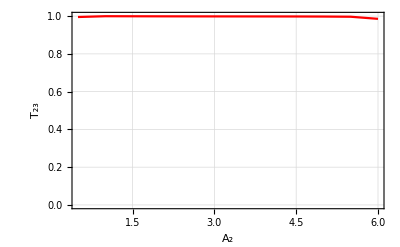
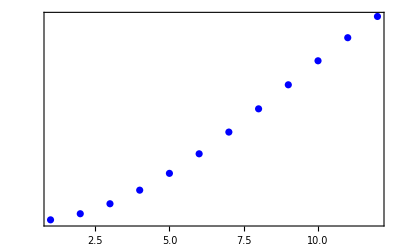
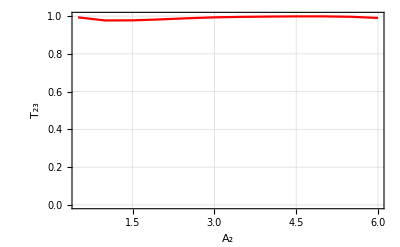
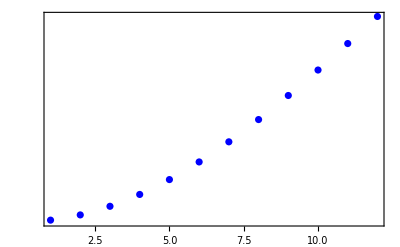
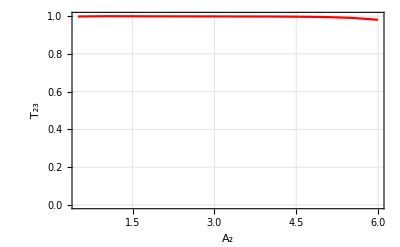
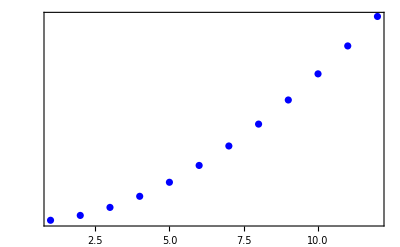
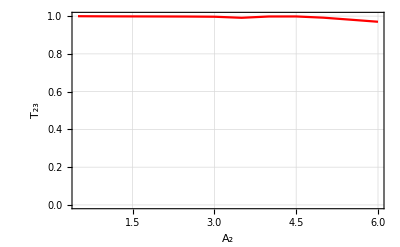
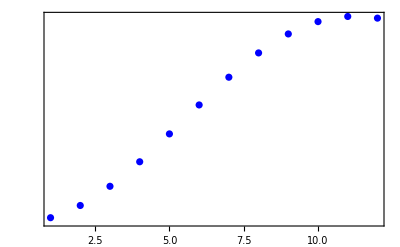
(-Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics-
-Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics-
-Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics-
-Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics-
-Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics-
-Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics-
-Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics-)

```mathematica
pchoice[[2,1;;7,1;;3]]//MatrixForm
```

-Graphics--Graphics-

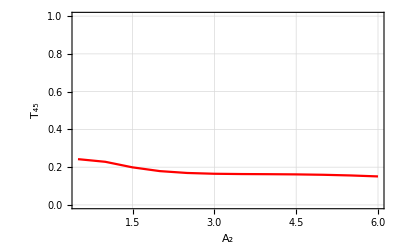
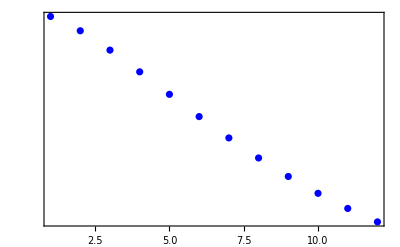

```mathematica
pchoice[[2,a1map[4],ϕmap[π/16]]]
pchoice[[4,a1map[4],ϕmap[π/16]]]
```

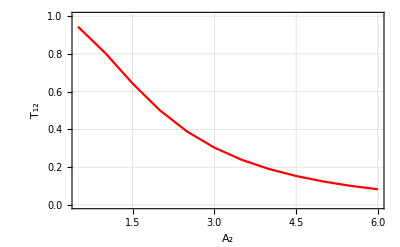
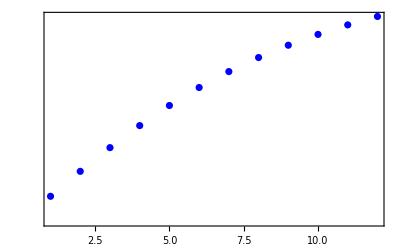

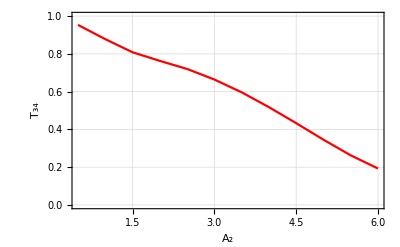
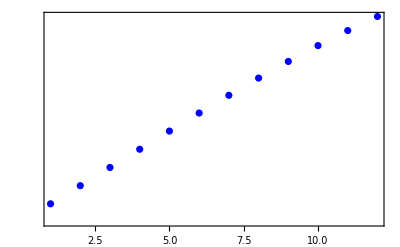

```mathematica
pchoice[[1,a1map[2],ϕmap[0]]]
pchoice[[3,a1map[2],ϕmap[0/16]]]
```

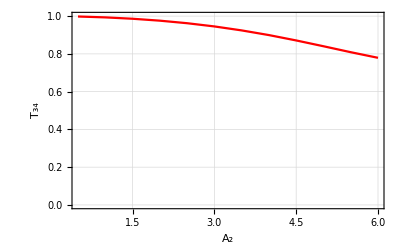
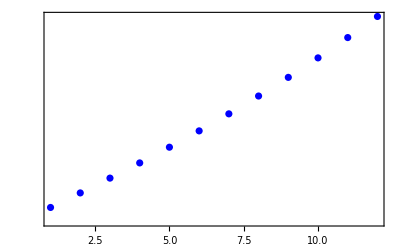
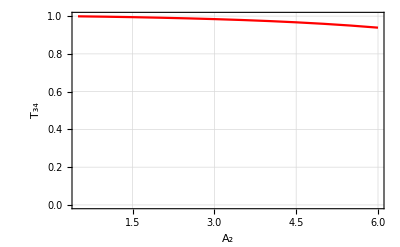
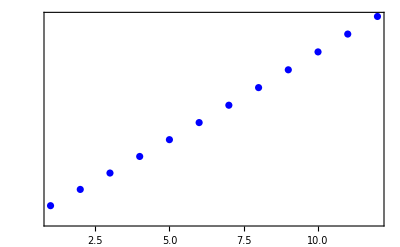
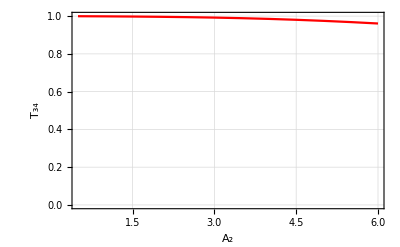
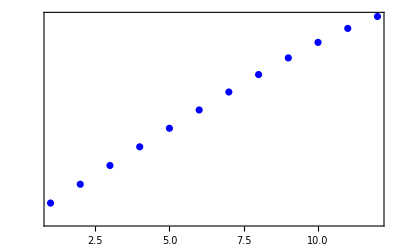
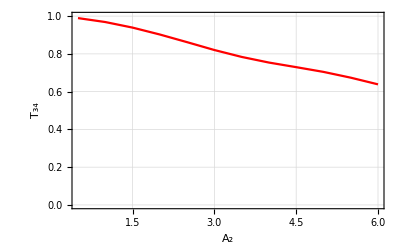
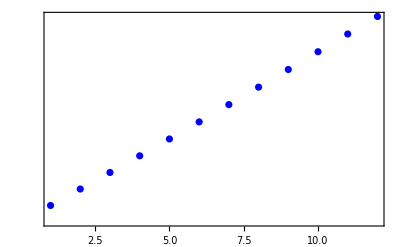
{{-Graphics--Graphics-,-Graphics--Graphics-,-Graphics--Graphics-},{-Graphics--Graphics-,-Graphics--Graphics-,-Graphics--Graphics-},{-Graphics--Graphics-,-Graphics--Graphics-,-Graphics--Graphics-},{-Graphics--Graphics-,-Graphics--Graphics-,-Graphics--Graphics-},{-Graphics--Graphics-,-Graphics--Graphics-,-Graphics--Graphics-},{-Graphics--Graphics-,-Graphics--Graphics-,-Graphics--Graphics-},{-Graphics--Graphics-,-Graphics--Graphics-,-Graphics--Graphics-}}

```mathematica
pchoice[[3]]
```

### 1→2 Transition for different forces

```mathematica
(*transition12allforce={{bg12f005,trans12f005,fullplots12f005},{bg12f01,trans12f01,fullplots12f01},{bg12f05,trans12f05,fullplots12f05},{bg12f1,trans12f1,fullplots12f1}};*)
```

```mathematica
fulltrans23={bg23f05,trans23f05,fullplots23f05};
fulltrans34={bg34f05,trans34f05,fullplots34f05};
fulltrans45={bg45f05,trans45f05,fullplots45f05};
```

```mathematica
ϕmap[ϕ_]:=If[ϕ==π/8,3,If[ϕ==π/16,2,1]];
a1map[a1_]:=If[a1==0.5,1,2*a1];
a2map[a2_]:=(ts=Solve[a2==0.5+fac(.25),fac];(fac+1)/.ts[[1]])
```

```mathematica
(*
A1∈{0.5, 1, 1.5}
ϕ∈{0, π/16, π/8}
*)
```

```mathematica
Dimensions[bg23f05]
```

{3,3,5}

```mathematica
allcrossings={fulltrans23,fulltrans34,fulltrans45};
```

```mathematica
fulltrans23//Dimensions
```

{2,3,3,5}

```mathematica
allcrossings[[3,3]]//Dimensions
```

{3,3,5}

```mathematica
AllPlots[transition_,a1_,a2_,angle_]:=ListPlot[allcrossings[[transition,3,ϕmap[angle],a1map[a1],a2map[a2]]]ᵀ,Joined->True,PlotRange->{0,1},GridLines->Automatic]
```

```mathematica
ShowMe[transition_,a1_,angle_]:=Overlay[{ListPlot[{allcrossings[[transition,2]][[ϕmap[angle],a1map[a1]]]},ImagePadding->45,PlotRange->{All,{0,1}},Frame->{{True,False},{True,True}},DataRange->{.5,2},FrameTicks->{{All,All},{{{.5,"0.5"},{1,"1"},{1.5,"1.5"},{2.,"2."}},None}},PlotStyle->Red,FrameStyle->{{{Red},None},{{Black},{Black}}},ImagePadding->30,PlotRange->All,Joined->True,FrameLabel->{"A_2","T_12"},FrameTicksStyle->{{{Red,15},{15}},{{Black,15},None}},LabelStyle->Directive[ 15],GridLines->{{0.5,0.75,1,1.25,1.5,1.75,2},Automatic}],ListPlot[allcrossings[[transition,1]][[ϕmap[angle],a1map[a1]]],ImagePadding->45,Frame->{{False,True},{False,False}},FrameTicks->{{None,All},{All,None}},PlotStyle->Blue,FrameStyle->Blue,ImagePadding->30,PlotRange->{All,All},Joined->False,FrameTicksStyle->{{None,{10}},{None,None}},FrameLabel->{{None,"Δ_12"},{None,None}},LabelStyle->Directive[ 10]]}];
```

```mathematica
fulltrans45//Dimensions
```

{3,3,3,5}

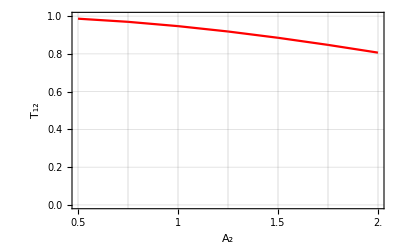
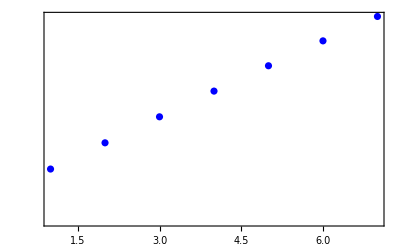
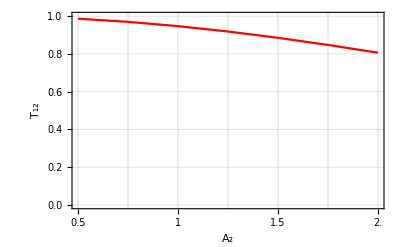
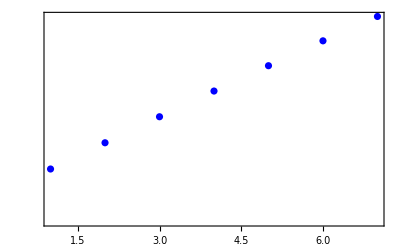
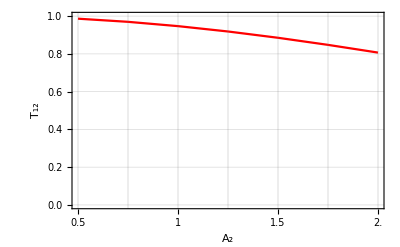
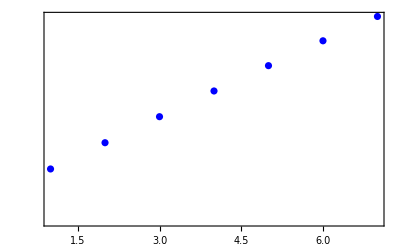
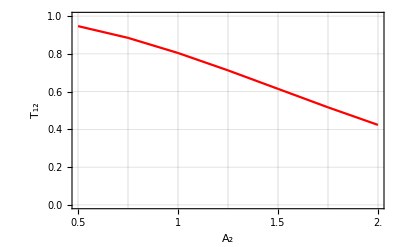
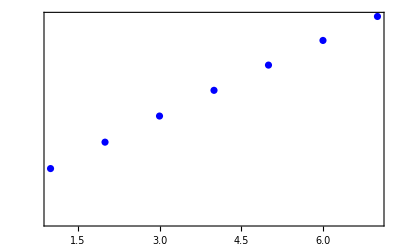

```mathematica
{{-Graphics--Graphics-,-Graphics--Graphics-,-Graphics--Graphics-},{-Graphics--Graphics-,-Graphics--Graphics-,-Graphics--Graphics-},{-Graphics--Graphics-,-Graphics--Graphics-,-Graphics--Graphics-},{-Graphics--Graphics-,-Graphics--Graphics-,-Graphics--Graphics-}}
```

{{-Graphics--Graphics-,-Graphics--Graphics-,-Graphics--Graphics-},{-Graphics--Graphics-,-Graphics--Graphics-,-Graphics--Graphics-},{-Graphics--Graphics-,-Graphics--Graphics-,-Graphics--Graphics-},{-Graphics--Graphics-,-Graphics--Graphics-,-Graphics--Graphics-}}

```mathematica
Dimensions[%102]
```

{4,3}

```mathematica
(*Export["12f05_phi0_a105.pdf",%102[[1,1]]]*)
(*Export["12f05_phi0_a11.pdf",%102[[2,1]]]*)
(*Export["12f05_phi0_a12.pdf",%102[[4,1]]]*)
(*Export["12f05_phipi8_a105.pdf",%102[[1,3]]]*)
(*Export["12f05_phipi8_a11.pdf",%102[[2,3]]]*)
Export["12f05_phi0_a115.pdf",%102[[3,1]]]
```

12f05_phi0_a115.pdf

```mathematica
transitionvalue[force_,ϕ_,a1_]:=transition12allforce[[forcemap[force],2,ϕmap[ϕ],a1map[a1]]];
```

```mathematica
transitionvalue[0.1,0,1]
```

{0.977026,0.94943,0.912751,0.86868,0.819073,0.765804,0.710638}

```mathematica
transitionvalue[0.05,0,2]
```

{0.807372,0.617988,0.424839,0.261144,0.141769,0.0661675,0.0252093}

```mathematica
transitionvalue[0.01,0,1]
```

{0.730216,0.492493,0.283297,0.138927,0.0583503,0.0215162,0.00757335}

```mathematica
transitionvalue[0.005,0,2]
```

{0.0827887,0.00454812,0.0000471496,0.0000932042,0.0000489165,0.000118572,0.000205043}

```mathematica
forcemap[0.1]
```

4

```mathematica
forcemap[0.01]
```

4

### Tunnelling between deep wells

```mathematica
grav=.354692 4;trunc=20;kr=π/4;nb=5;n=2000;
deepwells[levels_,A1_,A2_,ϕ_]:=(
(*If[levels[[1]]==1||levels[[1]]==3,ϕ=π/8,ϕ=0];*)F=grav;(*A1=a1;A2=a2;ϕ=phi;*)
H[κ_]=SparseArray[{{i_,i_}/;i≤trunc->((κ/π-1/2 trunc+1/2(i-1))^2-A1/2 - A2/2),{i_,i_}/;i==trunc+1->(κ/π+0)^2-A1/2 - A2/2,{i_,i_}/;i>trunc+1->(κ/π+1/2(i-trunc-1))^2-A1/2 - A2/2,{i_,j_}/;Abs[i-j]==4->-A1/4,{i_,j_}/;i-j==-5->-1/4 A2 ⅇ^(2 ⅈ ϕ),{i_,j_}/;i-j==5->-1/4 A2 ⅇ^(-2 ⅈ ϕ)},{2.trunc+1.,2.trunc+1.}];
reducedH[κ_]=H[κ]-IdentityMatrix[2trunc+1]*10^3;
fbz=Range[0,2kr,2kr/n][[1;;n]]//N;
Δk=fbz[[2]];
Δt=Δk/F;
values={};vectors={};
Do[
{e,v}=-Eigensystem[-reducedH[fbz[[i]]],10,Method->{"Arnoldi",Criteria->RealPart}];

Do[
α=Arg[v[[jk,trunc]]];
v[[jk]] = v[[jk]] Exp[-I α];

,{jk,10}];
Table[If[i>1&&Abs[(v[[ij]]-Last[vectorsᵀ[[ij]]])//Total]>1,v[[ij]]=-v[[ij]]],{ij,1,nb}];
AppendTo[values,e+10^3];
AppendTo[vectors,v];,
{i,1,n}];
x12={};
Do[nd=(vectors[[i+1,2]]-vectors[[i-1,2]])/(2Δk);
AppendTo[x12,nd.(vectors[[i,1]]*)];,{i,2,n-1}];
nx12=Join[{2x12[[1]]-x12[[2]]},x12,{-x12[[n-3]]+2x12[[n-2]]}];

x13={};
Do[nd=(vectors[[i+1,3]]-vectors[[i-1,3]])/(2Δk);
AppendTo[x13,nd.(vectors[[i,1]]*)];,{i,2,n-1}];
nx13=Join[{2x13[[1]]-x13[[2]]},x13,{-x13[[n-3]]+2x13[[n-2]]}];

x14={};
Do[nd=(vectors[[i+1,4]]-vectors[[i-1,4]])/(2Δk);
AppendTo[x14,nd.(vectors[[i,1]]*)];,{i,2,n-1}];
nx14=Join[{2x14[[1]]-x14[[2]]},x14,{2x14[[n-3]]-x14[[n-2]]}];

x15={};
Do[nd=(vectors[[i+1,5]]-vectors[[i-1,5]])/(2Δk);
AppendTo[x15,nd.(vectors[[i,1]]*)];,{i,2,n-1}];
nx15=Join[{2x15[[1]]-x15[[2]]},x15,{2x15[[n-3]]-x15[[n-2]]}];

x23={};
Do[nd=(vectors[[i+1,3]]-vectors[[i-1,3]])/(2Δk);
AppendTo[x23,nd.(vectors[[i,2]]*)];,{i,2,n-1}];
nx23=Join[{2x23[[1]]-x23[[2]]},x23,{-x23[[n-3]]+2x23[[n-2]]}];

x24={};
Do[nd=(vectors[[i+1,4]]-vectors[[i-1,4]])/(2Δk);
AppendTo[x24,nd.(vectors[[i,2]]*)];,{i,2,n-1}];
nx24=Join[{2x24[[1]]-x24[[2]]},x24,{2x24[[n-3]]-x24[[n-2]]}];

x25={};
Do[nd=(vectors[[i+1,5]]-vectors[[i-1,5]])/(2Δk);
AppendTo[x25,nd.(vectors[[i,2]]*)];,{i,2,n-1}];
nx25=Join[{2x25[[1]]-x25[[2]]},x25,{2x25[[n-3]]-x25[[n-2]]}];

x34={};
Do[nd=(vectors[[i+1,4]]-vectors[[i-1,4]])/(2Δk);
AppendTo[x34,nd.(vectors[[i,3]]*)];,{i,2,n-1}];
nx34=Join[{2x34[[1]]-x34[[2]]},x34,{2x34[[n-3]]-x34[[n-2]]}];
x35={};
Do[nd=(vectors[[i+1,5]]-vectors[[i-1,5]])/(2Δk);
AppendTo[x35,nd.(vectors[[i,3]]*)];,{i,2,n-1}];
nx35=Join[{2x35[[1]]-x35[[2]]},x35,{2x35[[n-3]]-x35[[n-2]]}];

x45={};
Do[nd=(vectors[[i+1,5]]-vectors[[i-1,5]])/(2Δk);
AppendTo[x45,nd.(vectors[[i,4]]*)];,{i,2,n-1}];
(*x45=-Abs[x45];*)
nx45=Join[{2x45[[1]]-x45[[2]]},x45,{2x45[[n-3]]-x45[[n-2]]}];
(*Landau Zener formula*)
gap[i_,j_]:=If[EvenQ[i],values[[1,j]]-values[[1,i]],values[[n/2,j]]-values[[n/2,i]]];
(*Number of half periods to take*)np=20;Tf=np kr/F;
(*Full Momentum Space Spanned*)
numericalxlists={nx12,nx13,nx14,nx15,nx23,nx24,nx25,nx34,nx35,nx45};
momenta=Table[k,{k,0,np kr,Δk}][[1;;n np/2]];

fullrange={dx12,dx13,dx14,dx15,dx23,dx24,dx25,dx34,dx35,dx45}={Table[{momenta[[i]],nx12[[Mod[i,n,1]]]},{i,n np/2}],Table[{momenta[[i]],nx13[[Mod[i,n,1]]]},{i,n np/2}],Table[{momenta[[i]],nx14[[Mod[i,n,1]]]},{i,n np/2}],Table[{momenta[[i]],nx15[[Mod[i,n,1]]]},{i,n np/2}],Table[{momenta[[i]],nx23[[Mod[i,n,1]]]},{i,n np/2}],Table[{momenta[[i]],nx24[[Mod[i,n,1]]]},{i,n np/2}],Table[{momenta[[i]],nx25[[Mod[i,n,1]]]},{i,n np/2}],Table[{momenta[[i]],nx34[[Mod[i,n,1]]]},{i,n np/2}],Table[{momenta[[i]],nx35[[Mod[i,n,1]]]},{i,n np/2}],
Table[{momenta[[i]],nx45[[Mod[i,n,1]]]},{i,n np/2}]};
fullrange={Abs[dx12],dx13,dx14,dx15,dx23//Abs,dx24,dx25,Abs[dx34],dx35,dx45};
correctingtable=Table[Table[If[Re[Sign[fullrange[[part]][[ i n,2]]]]=!=Re[Sign[fullrange[[part]][[i n+1,2]]]],fullrange[[part]][[i n+1;;(i+1)n,2]]=-fullrange[[part]][[i n+1;;(i+1)n,2]]],{i,1,np/2-1}],{part,{3,5,7}}];

overlaps={X12,X13,X14,X15,X23,X24,X25,X34,X35,X45}=Table[Interpolation[fullrange[[i]]],{i,1,Length[fullrange]}];
(*plotsRe=Table[Plot[overlaps[[i]][F t]//Re,{t,0,Tf},PlotRange->All,PlotStyle->If[i==1||i==5||i==8||i==10,Red,Blue]],{i,Length[overlaps]}];
plotsIm=Table[Plot[overlaps[[i]][F t]//Im,{t,0,Tf},PlotRange->All,PlotStyle->If[i==1||i==5||i==8||i==10,Red,Blue]],{i,Length[overlaps]}];*)

energy={ev1,ev2,ev3,ev4,ev5}=Table[Table[{momenta[[ii]],valuesᵀ[[bi,Mod[ii,n,1]]]},{ii,n np/2}],{bi,nb}];
bands[k_]={e1[k_],e2[k_],e3[k_],e4[k_],e5[k_]}=Table[Fit[energy[[bi]],Table[Cos[m 4k],{m,0,10}],k],{bi,nb}];
phases[t_]={p12[t],p13[t],p14[t],p15[t],p23[t],p24[t],p25[t],p34[t],p35[t],p45[t]}={Exp[- ⅈ Integrate[e1[F τ]-e2[F τ],{τ,0,t}]],Exp[- ⅈ Integrate[e1[F τ]-e3[F τ],{τ,0,t}]],Exp[- ⅈ Integrate[e1[F τ]-e4[F τ],{τ,0,t}]],Exp[- ⅈ Integrate[e1[F τ]-e5[F τ],{τ,0,t}]],Exp[- ⅈ Integrate[e2[F τ]-e3[F τ],{τ,0,t}]],Exp[- ⅈ Integrate[e2[F τ]-e4[F τ],{τ,0,t}]],Exp[- ⅈ Integrate[e2[F τ]-e5[F τ],{τ,0,t}]],Exp[- ⅈ Integrate[e3[F τ]-e4[F τ],{τ,0,t}]],Exp[- ⅈ Integrate[e3[F τ]-e5[F τ],{τ,0,t}]],Exp[- ⅈ Integrate[e4[F τ]-e5[F τ],{τ,0,t}]]};

phplotsRe=Table[Plot[phases[t][[i]]//Re,{t,0,Tf},PlotRange->All,PlotStyle->If[i==1||i==5||i==8||i==10,Red,Blue]],{i, Length[phases[t]]}];
phplotsIm=Table[Plot[phases[t][[i]]//Im,{t,0,Tf},PlotRange->All,PlotStyle->If[i==1||i==5||i==8||i==10,Red,Blue]],{i, Length[phases[t]]}];
phplotsAbs=Table[Plot[Abs[phases[t][[i]]],{t,0,Tf},PlotRange->All,PlotStyle->If[i==1||i==5||i==8||i==10,Red,Blue]],{i, Length[phases[t]]}];

(*If[levels[[1]]==1||levels[[1]]==3,{it=0,ft=Tf/2},{it=π/(4F),ft=3π/(4F)}];*)
start=Table[KroneckerDelta[levels[[1]],l],{l,1,nb}];
it=0;ft=Tf;

A=  F ({{0, X12[F t]p12[t], X13[F t]p13[t], X14[F t]p14[t], X15[F t]p15[t]}, {X12[F t]*p12[t]*, 0, X23[F t]p23[t], X24[F t]p24[t], X25[F t]p25[t]}, {X13[F t]*p13[t]*, X23[F t]*p23[t]*, 0, X34[F t]p34[t], X35[F t]p35[t]}, {X14[F t]*p14[t]*, X24[F t]*p24[t]*, X34[F t]*p34[t]*, 0, X45[F t]p45[t]}, {X15[F t]*p15[t]*, X25[F t]*p25[t]*, X35[F t]*p35[t]*, X45[F t]*p45[t]*, 0}});
initc={c1[it]==start[[1]],c2[it]==start[[2]],c3[it]==start[[3]],c4[it]==start[[4]],c5[it]==start[[5]]};
c={c1[t],c2[t],c3[t],c4[t],c5[t]};
eee= ⅈ D[c,t]-A.c;
eq=Table[eee[[hj]]==0,{hj,nb}];
sol=NDSolve[{Join[eq,initc]},{c1[t],c2[t],c3[t],c4[t],c5[t]},{t,it,ft}];
populations=Abs[(c/.sol)[[1]]]^2;
plot=Labeled[Plot[populations,{t,0,Tf},Frame->True,PlotStyle->{{Thickness[0.03]},{Thickness[0.03],Dashing[{0,Large}]},{Thickness[0.03],Dashing[{0.075,Large}]},{Thickness[0.03],Dashing[{0,Large,Large,Large}]}},FrameTicks->{{All,None},{{{0,"0"},{(2kr)/F,"1"},{4 kr/F,"2"},{6 kr/F,"3"},{8 kr/F,"4"}},None}},FrameTicksStyle->{{{Black,40},{40}},{{Black,40},None}},LabelStyle->Directive[ 40],GridLines->{None, {0,1}}],{Style["        t/SubsuperscriptBox[\"τ\", \"B\", 
 StyleBox[\"super\",\nFontSlant->\"Italic\"]]",FontFamily->"Times"],Style["|c_α(t)|^2",FontFamily->"Times"]},All,RotateLabel->False,LabelStyle->{FontSize->45}];)
```

```mathematica
Quiet[deepwells[{1,2},8,5,π/8];Pop12=populations;
deepwells[{2,3},8,5,0];Pop23=populations;
deepwells[{3,4},8,5,π/8];Pop34=populations;]
```

```mathematica
Quiet[deepwells[{1,2},15,10,π/8];Pop12deeper=populations;
deepwells[{2,3},15,10,0];Pop23deeper=populations;
deepwells[{3,4},15,10,π/8];Pop34deeper=populations;]
```

```mathematica
deepwells[{2,3},8,5,0];Pop23=populations;
```

```mathematica
{ii,bi,i,t}//Dynamic
```

```mathematica
p1=Labeled[Plot[Pop12,{t,0,Tf},Frame->True,FrameStyle->Directive[Black,Thick],PlotStyle->{{Thickness[0.015]},{Thickness[0.015],Dashing[{0,Medium}]},{Thickness[0.01],Dashing[{0.1,Medium
}]},{Thickness[0.01],Dashing[{0,Small,Medium,Small}]}},PlotLegends->Placed[{Style["α=1",FontFamily->"Times New Roman",FontSlant->Plain,FontSize->25],Style["α=2",FontFamily->"Times New Roman",FontSlant->Plain,FontSize->25](*,Style["α=3",FontFamily->"Times New Roman",FontSlant->Plain,FontSize->25],Style["α=4",FontFamily->"Times New Roman",FontSlant->Plain,FontSize->25],Style["α=5",FontFamily->"Times New Roman",FontSlant->Plain,FontSize->25]*)},Right],FrameTicks->{{All,None},{(*{{0,"0"},{(2kr)/F,"1"},{4 kr/F,"2"},{6 kr/F,"3"},{8 kr/F,"4"}}*)All,None}},Epilog->Inset[Style["(a)",FontSize->28,FontFamily->"Times New Roman",FontSlant->Italic],{9.5,0.5},{Left,Center}],FrameTicksStyle->{{{Black,30},{30}},{{Black,FontOpacity->1000,30},None}},LabelStyle->Directive["Times New Roman" ,35],GridLines->{None, {0,1}}],{Style["t/t_B",FontFamily->"Times New Roman",FontOpacity->1000],Style["|c_α(t)|^2",FontFamily->"Times New Roman"]},All,RotateLabel->False,LabelStyle->Directive[FontSize->35,FontSlant->Italic]]
```

-Graphics-t/t_B|c_α(t)|^2

```mathematica
p2=Labeled[Plot[Pop23,{t,0,Tf},Frame->True,FrameStyle->Directive[Black,Thick],PlotStyle->{{Thickness[0.015]},{Thickness[0.015],Dashing[{0,Medium}]},{Thickness[0.01],Dashing[{0.1,Medium
}]},{Thickness[0.01],Dashing[{0,Small,Medium,Small}]}},PlotLegends->Placed[{None,Style["α=2",FontFamily->"Times New Roman",FontSlant->Plain,FontSize->25],Style["α=3",FontFamily->"Times New Roman",FontSlant->Plain,FontSize->25](*,Style["α=4",FontFamily->"Times New Roman",FontSlant->Plain,FontSize->25],Style["α=5",FontFamily->"Times New Roman",FontSlant->Plain,FontSize->25]*)},After],Epilog->Inset[Style["(b)",FontSize->28,FontFamily->"Times New Roman",FontSlant->Italic],{10.2,0.5},{Left,Center}],FrameTicks->{{All,None},{(*{{0,"0"},{(2kr)/F,"1"},{4 kr/F,"2"},{6 kr/F,"3"},{8 kr/F,"4"}}*)All,None}},FrameTicksStyle->{{{Black,30,FontOpacity->0},{30}},{{Black,FontOpacity->1000,30},None}},LabelStyle->Directive["Times New Roman" ,35],GridLines->{None, {0,1}}],{Style["t/t_B",FontFamily->"Times New Roman"],Style["|c_α(t)|^2",FontFamily->"Times New Roman",FontOpacity->0]},All,RotateLabel->False,LabelStyle->Directive[FontSize->35,FontSlant->Italic,FontOpacity->100]]
```

-Graphics-t/t_B|c_α(t)|^2

```mathematica
p3new=Labeled[Plot[{100,100,100,100,100,Total[Pop12[[1;;2]]],Total[Pop23[[2;;3]]],Total[Pop34[[3;;4]]]},{t,0,Tf},PlotTheme->"Detailed",PlotStyle->{{Thickness[.01]},{Thickness[.0075],Dashed},{Thickness[.01],Dotted}},Frame->True,FrameStyle->Directive[Black,Thick],PlotRange->{.93,1.005},PlotLegends->Placed[{None,None,None,None,None,None,Style["A_1=E_R",FontFamily->"Times New Roman",FontSlant->Italic,FontSize->19],Style["A_1=2E_R",FontFamily->"Times New Roman",FontSlant->Italic,FontSize->19],Style["A_1=3E_R",FontFamily->"Times New Roman",FontSlant->Italic,FontSize->19]},{Left,Bottom}],FrameTicks->{{All,None},{(*{{0,"0"},{(2kr)/F,"1"},{4 kr/F,"2"},{6 kr/F,"3"},{8 kr/F,"4"}}*)All,None}},FrameTicksStyle->{{{Black,30,FontOpacity->100},{30}},{{Black,FontOpacity->100,30},None}},LabelStyle->Directive["Times New Roman" ,35],GridLines->{None, {0,1}}],{Style["t/t_B",FontFamily->"Times New Roman"],Style["|c_α(t)|^2+|c_β(t)|^2",FontFamily->"Times New Roman"]},All,RotateLabel->True,LabelStyle->Directive[FontSize->32,FontSlant->Italic,FontOpacity->100]]
```

-Graphics-t/t_B|c_α(t)|^2+|c_β(t)|^2

```mathematica
Export["deep_otal.pdf",p3new]
```

deep_otal.pdf

```mathematica
Plot[{Total[Pop12[[1;;2]]],Total[Pop23[[2;;3]]],Total[Pop34[[3;;4]]]},{t,0,Tf},PlotTheme->"Business",Frame->True,FrameStyle->Directive[Thick,Black]]
```

-Graphics-

```mathematica
Plot[Total[Pop34deeper[[3;;4]]],{t,0,Tf}]
```

-Graphics-

```mathematica
p3=Labeled[Plot[Pop34,{t,0,Tf},Frame->True,FrameStyle->Directive[Black,Thick],PlotStyle->{{Thickness[0.015]},{Thickness[0.015],Dashing[{0,Medium}]},{Thickness[0.01],Dashing[{0.1,Medium
}]},{Thickness[0.01],Dashing[{0,Small,Medium,Small}]}},PlotLegends->Placed[{None,None,Style["α=3",FontFamily->"Times New Roman",FontSlant->Plain,FontSize->25],Style["α=4",FontFamily->"Times New Roman",FontSlant->Plain,FontSize->25](*,Style["α=4",FontFamily->"Times New Roman",FontSlant->Plain,FontSize->25],Style["α=5",FontFamily->"Times New Roman",FontSlant->Plain,FontSize->25]*)},After],FrameTicks->{{All,None},{(*{{0,"0"},{(2kr)/F,"1"},{4 kr/F,"2"},{6 kr/F,"3"},{8 kr/F,"4"}}*)All,None}},Epilog->Inset[Style["(c)",FontSize->28,FontFamily->"Times New Roman",FontSlant->Italic],{9.,0.5},{Left,Center}],FrameTicksStyle->{{{Black,30,FontOpacity->100},{30}},{{Black,FontOpacity->100,30},None}},LabelStyle->Directive["Times New Roman" ,35],GridLines->{None, {0,1}}],{Style["t/t_B",FontFamily->"Times New Roman"],Style["|c_α(t)|^2",FontFamily->"Times New Roman"]},All,RotateLabel->False,LabelStyle->Directive[FontSize->35,FontSlant->Italic,FontOpacity->100]]
```

-Graphics-t/t_B|c_α(t)|^2

```mathematica
Export["deep1.pdf",p1];Export["deep2.pdf",p2];Export["deep3.pdf",p3];
```

```mathematica
p1=Labeled[Plot[Pop12deeper,{t,0,Tf},Frame->True,PlotStyle->{{Thickness[0.015]},{Thickness[0.015],Dashing[{0,Medium}]},{Thickness[0.01],Dashing[{0.075,Large}]},{Thickness[0.01],Dashing[{0,Small,Medium,Small}]}},FrameTicks->{{All,None},{(*{{0,"0"},{(2kr)/F,"1"},{4 kr/F,"2"},{6 kr/F,"3"},{8 kr/F,"4"}}*)All,None}},FrameTicksStyle->{{{Black,30},{30}},{{Black,30},None}},LabelStyle->Directive["Times New Roman" ,35],GridLines->{None, {0,1}}],{Style["        t/t_B",FontFamily->"Times New Roman"],Style["|c_α(t)|^2",FontFamily->"Times New Roman"]},All,RotateLabel->False,LabelStyle->Directive[FontSize->35,FontSlant->Italic]]
```

-Graphics-        t/t_B|c_α(t)|^2

```mathematica
p2=Labeled[Plot[Pop23deeper,{t,0,Tf},Frame->True,PlotStyle->{{Thickness[0.015]},{Thickness[0.015],Dashing[{0,Medium}]},{Thickness[0.01],Dashing[{0.055,Large}]},{Thickness[0.01],Dashing[{0,Small,Medium,Small}]}},FrameTicks->{{All,None},{(*{{0,"0"},{(2kr)/F,"1"},{4 kr/F,"2"},{6 kr/F,"3"},{8 kr/F,"4"}}*)All,None}},FrameTicksStyle->{{{Black,30},{30}},{{Black,30},None}},LabelStyle->Directive["Times New Roman" ,35],GridLines->{None, {0,1}}],{Style["        t/t_B",FontFamily->"Times New Roman"],Style["|c_α(t)|^2",FontFamily->"Times New Roman"]},All,RotateLabel->False,LabelStyle->Directive[FontSize->35,FontSlant->Italic]]
```

-Graphics-        t/t_B|c_α(t)|^2

```mathematica
p3=Labeled[Plot[Pop34//Evaluate,{t,0,Tf},Frame->True,PlotStyle->{{Thickness[0.015]},{Thickness[0.015],Dashing[{0,Medium}]},{Thickness[0.01],Dashing[{0.075,Large}]},{Thickness[0.01],Dashing[{0,Small,Medium,Small}]}},FrameTicks->{{All,None},{(*{{0,"0"},{(2kr)/F,"1"},{4 kr/F,"2"},{6 kr/F,"3"},{8 kr/F,"4"}}*)All,None}},FrameTicksStyle->{{{Black,30},{30}},{{Black,30},None}},LabelStyle->Directive["Times New Roman" ,35],GridLines->{None, {0,1}}],{Style["        t/t_B",FontFamily->"Times New Roman"],Style["|c_α(t)|^2",FontFamily->"Times New Roman"]},All,RotateLabel->False,LabelStyle->Directive[FontSize->35,FontSlant->Italic]]
```

-Graphics-        t/t_B|c_α(t)|^2

```mathematica
Total[Pop23[[2;;3]]/.t->Tf]
```

0.936957

```mathematica
{i,ii,bi,τ}//Dynamic
```

```mathematica
populations//Dimensions
```

{}

```mathematica
p12[F t]
```

p12[1.41877 t]

```mathematica
tab=Table[{t,populations[[1]]},{t,0,Tf,Δt}];
ds=Sort[tabᵀ[[2]]][[1]];pos=Position[tab,ds][[1,1]];
tab[[pos]]
```

{2.63348,0.00379902}

```mathematica
deepwells[{2,3},8,5,π/20];
```

InterpolatingFunction::dmval: Input value {15.708} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

```mathematica
Table[populations[[2]],{t,0,Tf,Δt}]//Min
```

0.973389

```mathematica
Labeled[Plot[{100,populations[[2]]},{t,0,Tf},Frame->True,FrameStyle->Directive[Black,Thick],PlotStyle->{{Thickness[0.015]},{Thickness[0.015],Dashing[{0,Medium}]},{Thickness[0.01],Dashing[{0.1,Medium
}]},{Thickness[0.01],Dashing[{0,Small,Medium,Small}]}},PlotRange->{.97,1.001},FrameTicks->{{All,None},{(*{{0,"0"},{(2kr)/F,"1"},{4 kr/F,"2"},{6 kr/F,"3"},{8 kr/F,"4"}}*)All,None}},FrameTicksStyle->{{{Black,30,FontOpacity->100},{30}},{{Black,FontOpacity->100,30},None}},LabelStyle->Directive["Times New Roman" ,35],GridLines->{None, {0,1}}],{Style["        t/t_B",FontFamily->"Times New Roman"],Style["|c_2(t)|^2",FontFamily->"Times New Roman"]},All,RotateLabel->False,LabelStyle->Directive[FontSize->35,FontSlant->Italic,FontOpacity->100]]
```

-Graphics-        t/t_B|c_2(t)|^2

```mathematica
Export["deepxfer2.pdf",%]
```

deepxfer2.pdf

```mathematica
Export["deep_xfer.pdf",Labeled[Plot[Evaluate[populations[[1;;2]]],{t,0,Tf},PlotRange->{.97,1},Frame->True,PlotStyle->{{Thickness[0.03]},{Thickness[0.03],Dashing[{0,Large}]},{Thickness[0.03],Dashing[{0.075,Large}]},{Thickness[0.03],Dashing[{0,Large,Large,Large}]}},FrameTicks->{{{{.97,.97},{.98,.98},{.99,.99},{1,1}},None},{{{0,"0"},{(8kr)/F,"4"},{4 kr/F,"2"},{12 kr/F,"6"},{16 kr/F,"8"},{20 kr/F,"10"}},None}},FrameTicksStyle->{{{Black,40},{40}},{{Black,40},None}},LabelStyle->Directive[ 40],GridLines->{None, {0,1}}],{Style["        t/SubsuperscriptBox[\"τ\", \"B\", 
 StyleBox[\"super\",\nFontSlant->\"Italic\"]]",FontFamily->"Times"],Style["|c_α(t)|^2",FontFamily->"Times"]},All,RotateLabel->False,LabelStyle->{FontSize->45}]]
```

deep_xfer.pdf

```mathematica
Export["deep_noxfer.pdf",deepwells[{2,3},8,5,π/20]]
```

```mathematica
deepwellscollective=Table[deepwells[levels,pot[[1]],pot[[2]],levels[[3]]],{levels,{{1,2,π/8},{2,3,0},{3,4,π/8}}},{pot,{{8,5}}}];
```

$Aborted

```mathematica
{pot,levels}//Dynamic
```

```mathematica
{i,t}//Dynamic
```

```mathematica
deepwells[{2,3},8,5,0/8]
```

InterpolatingFunction::dmval: Input value {6.28319} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

-Graphics-        t/τ_B^super|c_α(t)|^2

```mathematica
Export["deep_23_grav.pdf",%63]
```

deep_23_grav.pdf

```mathematica
Export["deep_23_grav.pdf",Labeled[Plot[populations,{t,0,Tf},Frame->True,PlotStyle->{{Thickness[0.03]},{Thickness[0.03],Dashing[{0,Large}]},{Thickness[0.03],Dashing[{0.075,Large}]},{Thickness[0.03],Dashing[{0,Large,Large,Large}]}},FrameTicks->{{All,None},{{{0,"0"},{(2kr)/F,"1"},{4 kr/F,"2"},{6 kr/F,"3"},{8 kr/F,"4"}},None}},FrameTicksStyle->{{{Black,40},{40}},{{Black,40},None}},LabelStyle->Directive[ 40],GridLines->{None, {0,1}}],{Style["        t/SubsuperscriptBox[\"τ\", \"B\", 
 StyleBox[\"super\",\nFontSlant->\"Italic\"]]",FontFamily->"Times"],Style["|c_α(t)|^2",FontFamily->"Times"]},All,RotateLabel->False,LabelStyle->{FontSize->45}]]
```

deep_23_grav.pdf

```mathematica
Export["deep_12_grav.pdf",deepwellscollective[[1,1]]]
Export["deep_23_grav.pdf",deepwellscollective[[2,1]]]
Export["deep_34_grav.pdf",deepwellscollective[[3,1]]]
```

deep_12_grav.pdf

deep_23_grav.pdf

deep_34_grav.pdf

### Band gaps vs phi

```mathematica
ClearAll
```

ClearAll

```mathematica
func[A1_,A2_]:=(grav=.354692 4;trunc=20;kr=π/4;nb=5;If[A1≤1||A2≤1,n=15000,n=5000];F=.1;(*A1=1.;A2=1;ϕ=π/8;*)
fbz=Range[0,2kr,2kr/n][[1;;n]]//N;
Δk=fbz[[2]];
Δt=Δk/F;H[κ_]=SparseArray[{{i_,i_}/;i≤trunc->((κ/π-1/2 trunc+1/2(i-1))^2-A1/2 - A2/2),{i_,i_}/;i==trunc+1->(κ/π+0)^2-A1/2 - A2/2,{i_,i_}/;i>trunc+1->(κ/π+1/2(i-trunc-1))^2-A1/2 - A2/2,{i_,j_}/;Abs[i-j]==4->-A1/4,{i_,j_}/;i-j==-5->-1/4 A2 ⅇ^(2 ⅈ ϕ),{i_,j_}/;i-j==5->-1/4 A2 ⅇ^(-2 ⅈ ϕ)},{2.trunc+1.,2.trunc+1.}];
reducedH[κ_]=H[κ]-IdentityMatrix[2trunc+1]*10^3;
gap12xphi={};gap23xphi={};gap34xphi={};gap45xphi={};gap56xphi={};
Do[
edgeofBZ=-Eigenvalues[-reducedH[kr],10,Method->{"Arnoldi",Criteria->RealPart}];
centreofBZ=-Eigenvalues[-reducedH[0],10,Method->{"Arnoldi",Criteria->RealPart}];
gap12=edgeofBZ[[2]]-edgeofBZ[[1]];
gap23=centreofBZ[[3]]-centreofBZ[[2]];
gap34=edgeofBZ[[4]]-edgeofBZ[[3]];
gap45=centreofBZ[[5]]-centreofBZ[[4]];
gap56=edgeofBZ[[6]]-edgeofBZ[[5]];
AppendTo[gap12xphi,gap12];
AppendTo[gap23xphi,gap23];
AppendTo[gap34xphi,gap34];
AppendTo[gap45xphi,gap45];AppendTo[gap56xphi,gap56];,{ϕ,0,π/4,π/128}];
plot=Labeled[ListPlot[{gap12xphi,gap23xphi,gap34xphi,gap45xphi,gap56xphi},DataRange->{0,π/4},Frame->{{True,True},{True,True}},FrameTicks->{{All,None},{{{0,"0"},{π/16,"π/16"},{π/8,"π/8"},(*{π/5,"π/5"},*){π/4,"π/4"},{3π/16,"(3  π)/16"}},None}},PlotRange->All,Joined->True,PlotStyle->Thickness[0.01],FrameTicksStyle->{{{Black,30},{30}},{{Black,30},None}},LabelStyle->Directive[ 45]],{Style["   ϕ",FontFamily->"Times"],Style["Δ_αβ/E_R",FontFamily->"Times"]},All,RotateLabel->False,LabelStyle->{FontSize->45}]
)
```

```mathematica
Export["bgvphi_sm_a1_pt5_a2_pt25_phi_0_to_pi8.pdf",func[0.5,0.25]];
Export["bgvphi_sm_a1_pt5_a2_3_phi_0_to_pi8.pdf",func[0.5,3]];
Export["bgvphi_sm_a1_2_a2_pt25_phi_0_to_pi8.pdf",func[2,.25]];
Export["bgvphi_sm_a1_2_a2_3_phi_0_to_pi8.pdf",func[2.,3.]];
```

$Aborted

```mathematica
func[8.,5.]
```

-Graphics-   ϕΔ_αβ/E_R

```mathematica
3.5*10^-3
```

0.0035

```mathematica
s
```

```mathematica
Min[gap23xphi]
```

0.00353019

```mathematica
Min[gap12xphi]
```

0.0592336

```mathematica
Min[gap34xphi]
```

0.0370957

```mathematica
func[2.,3.]
```

-Graphics-   ϕΔ_αβ/E_R

```mathematica
func[8.,5.]
```

-Graphics-   ϕΔ_αβ/E_R

```mathematica
ff=Labeled[ListPlot[{gap12xphi,gap23xphi,gap34xphi,gap45xphi},DataRange->{0,π/4},Frame->{{True,True},{True,True}},FrameStyle->Directive[Thick,Black],FrameTicks->{{Automatic,None},{{{0,"0"},{π/16,"π/16"},{π/8,"π/8"},(*{π/5,"π/5"},*){π/4,"π/4"},{3π/16,"(3  π)/16"}},None}},PlotRange->All,Joined->True,PlotStyle->{{Thickness[0.01]},{Thickness[0.01],Dashing[.025]},{Thickness[0.01],Dashing[{0.005,Medium}]},{Thickness[0.01],DotDashed}},PlotLegends->Placed[{Style["Δ",FontFamily->"Times New Roman",FontSize->25],Style["Δ",FontFamily->"Times New Roman",FontSize->25],Style["Δ",FontFamily->"Times New Roman",FontSize->25],Style["Δ",FontFamily->"Times New Roman",FontSize->25]},Right],(*Epilog->Inset[Framed[Style["Spiral",40],Background->LightYellow],{.1,.1}],*)FrameTicksStyle->Directive[Black,Label,30],LabelStyle->Directive[25]],{Style["ϕ         ",FontFamily->"Times New Roman",FontSize->35,FontSlant->Plain],Style["Δ_αβ/E_R",FontFamily->"Times New Roman",FontSize->45,FontSlant->Italic]},{Bottom,Left},RotateLabel->False,LabelStyle->{FontSize->45}]
```

-Graphics-ϕ         Δ_αβ/E_R

```mathematica
Export["bandgapvsphi.pdf",ff]
```

bandgapvsphi.pdf

```mathematica
func2[band1_]:=(grav=.354692 4;trunc=20;kr=π/4;nb=5;n=1000;
F=.1;If[band1==1||band1==3,ϕ=π/8,ϕ=0];
fbz=Range[0,2kr,2kr/n][[1;;n]]//N;
Δk=fbz[[2]];
Δt=Δk/F;
ll={};
Do[
H[κ_]=SparseArray[{{i_,i_}/;i≤trunc->((κ/π-1/2 trunc+1/2(i-1))^2-A1/2 - A2/2),{i_,i_}/;i==trunc+1->(κ/π+0)^2-A1/2 - A2/2,{i_,i_}/;i>trunc+1->(κ/π+1/2(i-trunc-1))^2-A1/2 - A2/2,{i_,j_}/;Abs[i-j]==4->-A1/4,{i_,j_}/;i-j==-5->-1/4 A2 ⅇ^(2 ⅈ ϕ),{i_,j_}/;i-j==5->-1/4 A2 ⅇ^(-2 ⅈ ϕ)},{2.trunc+1.,2.trunc+1.}];
reducedH[κ_]=H[κ]-IdentityMatrix[2trunc+1]*10^3;
Ev=Table[-Eigenvalues[-reducedH[fbz[[i]]],5,Method->{"Arnoldi",Criteria->RealPart}],{i,n}];

Ev=Ev+10^3;

DiffBands=Abs[Evᵀ[[band1]]-Evᵀ[[band1+1]]];
Avg=Mean[DiffBands];Smallest=Min[DiffBands];
AppendTo[ll,{A1,A2,Abs[Avg-Smallest]}];

,{A1,1,10,.5},{A2,1,10,.5}];
)

func2[1]
```

```mathematica
ListContourPlot[ll,PlotRange->{0,.005},PlotLegends->Automatic]
```

-Graphics-